## Load and Prepare Audio for Feature Extraction

Audio are loaded, resampled to 16 Khz , and chunked to 0.96s windows (both required by YAMNet).

```mathematica
(* Define the directories *)
nopoiDirectory="/Users/jcromwell/Library/CloudStorage/GoogleDrive-jcromwell@entacmedical.com/Shared drives/*Master Drive - ABJ/*Master Folder - Entac/R&D/PrevisAI/files/12h/nopoi/foreground";
poiDirectory="/Users/jcromwell/Library/CloudStorage/GoogleDrive-jcromwell@entacmedical.com/Shared drives/*Master Drive - ABJ/*Master Folder - Entac/R&D/PrevisAI/files/12h/poi/foreground";

(* Get the list of audio files *)
nopoiFiles=FileNames["*.wav",nopoiDirectory];
poiFiles=FileNames["*.wav",poiDirectory];

(*Convert to single channel and resample at 16KHz*)
resampledNoPOI=AudioResample[AudioChannelMix[Import[#],"Mono"],16000]&/@nopoiFiles;
resampledPOI=AudioResample[AudioChannelMix[Import[#],"Mono"],16000]&/@poiFiles;
```

## Audio Augmentation

```mathematica
augmentAudio[audio_Audio,n_Integer]:=Table[Module[{tempAudio=audio,choice=RandomInteger[{1,3}],noiseAudio,scaledNoise},Switch[choice,1,(*Pitch Shift with Bug Workaround*)Module[{direction=RandomChoice[{-1,1}],amount=RandomReal[{0.1,1.5}]},If[direction==1,tempAudio=AudioPitchShift[tempAudio,amount],tempAudio=AudioReverse[AudioPitchShift[AudioReverse[tempAudio],amount]]]],2,(*Time Stretch*)tempAudio=AudioTimeStretch[tempAudio,RandomReal[{0.9,1.1}]],3,(*Add Noise with Explicit Sampling*)(*Create noise audio directly with AudioGenerator*)noiseAudio=AudioGenerator[RandomChoice[{"White","Pink","Brown"}],Duration[audio],SampleRate->16000];
(*Scale the noise and overlay*)scaledNoise=AudioAmplify[noiseAudio,RandomReal[{0.01,0.05}]];
tempAudio=AudioOverlay[{tempAudio,scaledNoise}]];
tempAudio],n]

augmentedPOI=Flatten[augmentAudio[#,5]&/@resampledPOI];
augmentedNoPOI=Flatten[augmentAudio[#,5]&/@resampledNoPOI];
```

```mathematica
combinedPOI=Join[resampledPOI,augmentedPOI];
combinedNoPOI=Join[resampledNoPOI,augmentedNoPOI];
```

## Feature Extractor

```mathematica
(*Import AudioIdentify V1 which is trained on same set as YAMNet*)
(*Modify the model for feature extraction*)
coreNet=NetExtract[NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"],{1,"Net"}];
singleFrameFeatureExtractor=NetDrop[coreNet,-3];
extractor=NetChain[{NetMapOperator[singleFrameFeatureExtractor],AggregationLayer[Max,1],FlattenLayer[]},"Input"->NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"][["Input"]]];
```

## Feature Extraction

```mathematica
counter=0;
featureVectorsPOI=Monitor[Map[(counter++;extractor[#])&,combinedPOI],Row[{ProgressIndicator[counter,{1,Length[combinedPOI]}]," Processing sample ",counter," of ",Length[combinedPOI]}]];
```

```mathematica
poiData=Thread[featureVectorsPOI->1];
```

```mathematica
counter=0;
featureVectorsNoPOI=Monitor[Map[(counter++;extractor[#])&,combinedNoPOI],Row[{ProgressIndicator[counter,{1,Length[combinedNoPOI]}]," Processing sample ",counter," of ",Length[combinedNoPOI]}]];
nopoiData=Thread[featureVectorsNoPOI->0];
```

## Stratified Split of Data

```mathematica
SeedRandom[];
stratifiedSplitFromGroups[poiData_List,nopoiData_List,poiTestCount_Integer:5]:=Module[{shuffledPOI,shuffledNoPOI,poiTrainFeatures,poiTestFeatures,noPoiTrainFeatures,noPoiTestFeatures,noPoiTestCount,trainPairs,testPairs,shuffledTrain,shuffledTest,xTrain,yTrain,xTest,yTest},(*1. Split the POI data (labeled 1)*)shuffledPOI=RandomSample[poiData];
poiTestFeatures=Take[shuffledPOI,poiTestCount];
poiTrainFeatures=Drop[shuffledPOI,poiTestCount];
(*2. Split the non-POI data (labeled 0) using the same proportion*)noPoiTestCount=Round[Length[nopoiData]*(Length[poiTestFeatures]/Length[poiData])];
shuffledNoPOI=RandomSample[nopoiData];
noPoiTestFeatures=Take[shuffledNoPOI,noPoiTestCount];
noPoiTrainFeatures=Drop[shuffledNoPOI,noPoiTestCount];
(*3. Create {feature,label} pairs for the training and test sets*)trainPairs=Join[Transpose[{poiTrainFeatures,ConstantArray[1,Length[poiTrainFeatures]]}],Transpose[{noPoiTrainFeatures,ConstantArray[0,Length[noPoiTrainFeatures]]}]];
testPairs=Join[Transpose[{poiTestFeatures,ConstantArray[1,Length[poiTestFeatures]]}],Transpose[{noPoiTestFeatures,ConstantArray[0,Length[noPoiTestFeatures]]}]];
(*4. Shuffle the pairs and separate back into features (X) and labels (y)*){xTrain,yTrain}=Transpose[RandomSample[trainPairs]];
{xTest,yTest}=Transpose[RandomSample[testPairs]];
(*5. Return an Association for clarity*)<|"XTrain"->xTrain,"yTrain"->yTrain,"XTest"->xTest,"yTest"->yTest|>];
poiFeatureVectors=First/@poiData;
nopoiFeatureVectors=First/@nopoiData;
splitData=stratifiedSplitFromGroups[poiFeatureVectors,nopoiFeatureVectors,5];
trainingData=Thread[splitData["XTrain"]->splitData["yTrain"]];
testData=Thread[splitData["XTest"]->splitData["yTest"]];
```

## Train Model

```mathematica
utf=UtilityFunction-> <|0-> <|0-> 1, 1-> -1|>,1-> <|1-> 1,0->-2|>|>;
classifier=Classify[trainingData,Method->"SupportVectorMachine",PerformanceGoal->"Quality"];
```

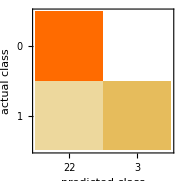
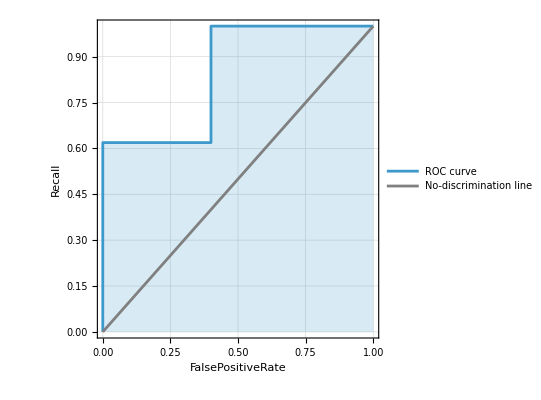
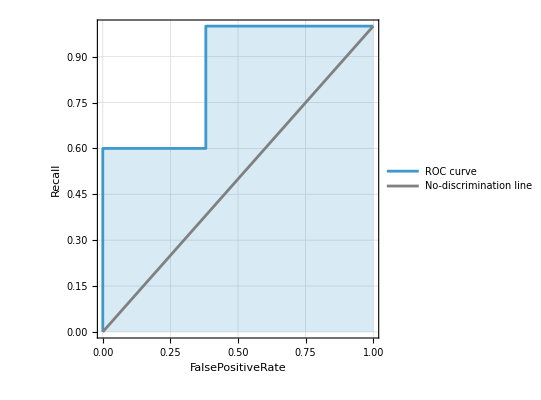
{-Graphics-,<|0→-Graphics-,1→-Graphics-|>,<|0→0.847619,1→0.847619|>}

```mathematica
measurements=ClassifierMeasurements[classifier,testData,{"ConfusionMatrixPlot","ROCCurve","AreaUnderROCCurve"},UtilityFunction-> <|0-> <|0-> 1, 1-> -1|>,1-> <|1-> 1,0->-20|>|>]
```

```mathematica
.
```